# Tufts Computational Physics

## Class 2

I've written this notebook to introduce some of the many plotting and ODE solving tools available in Mathematica. We begin with a look at the simple pendulum, comparing an analytical, linearized and numerical solution. In the second section, I provide an outline for you to write your own iterative solver that we’ll work on in class together.

## The Simple Pendulum

The simple pendulum obeys the equation

	θ’’(t)+ k^2sin(θ(t)) =0

together with initial conditions:—

θ(0) = θ_0 — initial position
k = Sqrt(g/L) — a parameter that measures the

We can write a function to integrate this numerically using NDSolve.

```mathematica
solve[k_,θ0_,T_]:=NDSolve[{D[θ[t],t,t]== -k^2 Sin[θ[t]],θ[0]==θ0,θ'[0]==0},θ[t],{t,0,T}]
```

and plot the solution.

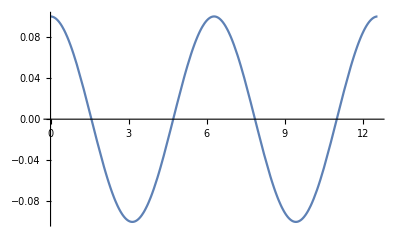

```mathematica
Plot[Evaluate[θ[t]/.solve[1,0.1,4Pi]],{t,0,4 Pi}]
```

Manipulate allows us to investigate the effect of varying parameters on the solution

```mathematica
Manipulate[Plot[Evaluate[θ[t]/.solve[k,θ0,4Pi]],{t,0,4 Pi},PlotRange-> {-1,1}],{{k,1},0.1,1},{{θ0,0.1},0,Pi/2}]
```

To make analytical progress, we linearize the equation

```mathematica
Normal[Series[D[θ[t],t,t]+k^2 Sin[θ[t]],{θ[t],0,1}]]
```

k^2 θ[t]+θ''[t]

obtaining the simple harmonic motion equation which can now be solved analytically using DSolve

```mathematica
ψlin=θ[t]/.DSolve[{D[θ[t],t,t]+ k^2 θ[t]==0,θ[0]==θ0,θ'[0]==0},θ[t],t]⟦1⟧
```

θ0 Cos[k t]

The nonlinear equation actually possesses an analytical solution in terms of Elliptic integrals

```mathematica
ψana=2 ArcSin[Sin[θ0/2] JacobiSN[EllipticK[Sin[θ0/2]^2]-k t,Sin[θ0/2]^2]]
```

2 ArcSin[JacobiCD[k t,Sin[θ0/2]^2] Sin[θ0/2]]

```mathematica
Manipulate[Plot[2 ArcSin[Sin[θ0/2] JacobiSN[EllipticK[Sin[θ0/2]^2]-k t,Sin[θ0/2]^2]],{t,0,4 Pi},PlotRange-> {-1/2,1/2}],{{k,1},0.1,1},{{θ0,0.1},0,Pi/2}]
```

Compare the three at low amplitude—they all overlap indicating good agreement

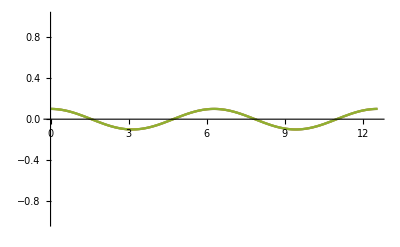

```mathematica
Plot[{Evaluate[θ[t]/.solve[1,0.1,4Pi]],ψana/.k-> 1/.θ0-> 0.1,ψlin/.k-> 1/.θ0-> 0.1},{t,0,4 Pi},PlotRange-> {-1,1}]
```

and at higher amplitude—the linearized solution incorrectly captures the period

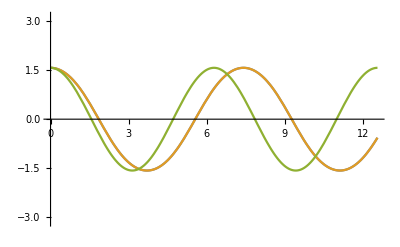

```mathematica
Plot[{Evaluate[θ[t]/.solve[1,Pi/2,4Pi]],ψana/.k-> 1/.θ0->Pi/2,ψlin/.k-> 1/.θ0-> Pi/2},{t,0,4 Pi},PlotRange-> {-Pi,Pi}]
```

At even higher amplitudes, the shape of the trajectory is quite different.

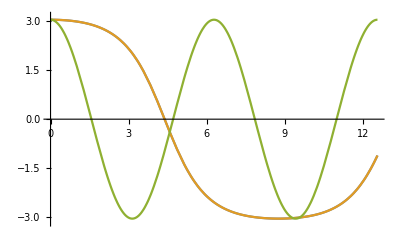

```mathematica
Plot[{Evaluate[θ[t]/.solve[1,Pi-0.1,4Pi]],ψana/.k-> 1/.θ0->Pi-0.1,ψlin/.k-> 1/.θ0-> Pi-0.1},{t,0,4 Pi},PlotRange-> {-Pi,Pi}]
```

## The Double Pendulum

Framework for a basic iterative integrator. Reap collects the output; Sow produces it.

```mathematica
tt=0; δt=0.1; theta=1;niter=100; (* Initial conditions *)

rr=Reap[
Do[

(* Update θ here *)
theta+=0.1;

tt+= δt; (* Update t *)
Sow[{tt,theta}]; (* Output *)

,{i,niter}]
];
```

Plot the output

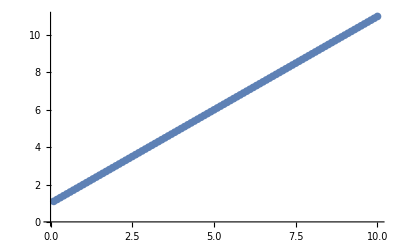

```mathematica
ListPlot[rr⟦2,1⟧]
```

Export the output

```mathematica
Export[NotebookDirectory[]<>"out.txt",rr⟦2,1⟧,"Table"];
```